```mathematica
G[u_,v_,J_,K_]:=(2*u*K)/(v-u+v*J+u*K+Sqrt[(v-u+v*J+u*K)^2-4*(v-u)*u*K]);

ACp[r1_,cAMP_,r2_,Dvalue_,Km1_,Km2_,ACt_]:=ACt*G[r1*cAMP,r2*Dvalue,Km1/ACt,Km2/ACt];

dPDEp[r3_,cAMP_,PDEt_,PDEp_,Km3_,r4_,Et_,Km4_]:=r3*cAMP*((PDEt-PDEp)/Km3)-r4*Et*PDEp/(Km4+PDEp);

dcAMP[k1_,ACp_,k3_,k2_,PDEp_,cAMP_]:=k1*ACp-(k3+k2*PDEp)*cAMP;

F1=dcAMP[k1,ACp[r1,cAMP,r2,Dvalue,Km1,Km2,ACt],k3,k2,PDEp,cAMP];
F2=dPDEp[r3,cAMP,PDEt,PDEp,Km3,r4,Et,Km4];

JacobianMatrix=D[{F1,F2},{{cAMP,PDEp}}]
```

{{-0.12-(349.824 cAMP (-2.04+19.0536/ACt+(-(76.2144 (11.7684-2.04 cAMP))/ACt+(155.477 cAMP)/ACt+2 (-2.04+19.0536/ACt) (11.7684+5.41346/ACt-2.04 cAMP+(19.0536 cAMP)/ACt))/(2 √(-(76.2144 (11.7684-2.04 cAMP) cAMP)/ACt+(11.7684+5.41346/ACt-2.04 cAMP+(19.0536 cAMP)/ACt)^2))))/((11.7684+5.41346/ACt-2.04 cAMP+(19.0536 cAMP)/ACt+√(-(76.2144 (11.7684-2.04 cAMP) cAMP)/ACt+(11.7684+5.41346/ACt-2.04 cAMP+(19.0536 cAMP)/ACt)^2))^2)+349.824/(11.7684+5.41346/ACt-2.04 cAMP+(19.0536 cAMP)/ACt+√(-(76.2144 (11.7684-2.04 cAMP) cAMP)/ACt+(11.7684+5.41346/ACt-2.04 cAMP+(19.0536 cAMP)/ACt)^2))-10 PDEp,-10 cAMP},{0.444444 (9.66-PDEp),-0.444444 cAMP+(3.7536 PDEp)/(0.18+PDEp)^2-3.7536/(0.18+PDEp)}}

```mathematica
SimplifiedJacobian=Simplify[JacobianMatrix]
```

{{-k3-k2 PDEp-(2 ACt^2 cAMP k1 Km2 r1^2 (-1+Km2/ACt+(2 ACt cAMP Km2 r1-ACt Dvalue (Km1+Km2) r2+ACt^2 (cAMP r1-Dvalue r2)+Km2 (cAMP Km2 r1+Dvalue Km1 r2))/(ACt^2 √((4 ACt cAMP Km2 r1 (cAMP r1-Dvalue r2)+(-ACt cAMP r1+cAMP Km2 r1+ACt Dvalue r2+Dvalue Km1 r2)^2)/ACt^2))))/((-ACt cAMP r1+cAMP Km2 r1+ACt Dvalue r2+Dvalue Km1 r2+ACt √((4 ACt cAMP Km2 r1 (cAMP r1-Dvalue r2)+(-ACt cAMP r1+cAMP Km2 r1+ACt Dvalue r2+Dvalue Km1 r2)^2)/ACt^2))^2)+(2 ACt k1 Km2 r1)/(-ACt cAMP r1+cAMP Km2 r1+ACt Dvalue r2+Dvalue Km1 r2+ACt √((4 ACt cAMP Km2 r1 (cAMP r1-Dvalue r2)+(-ACt cAMP r1+cAMP Km2 r1+ACt Dvalue r2+Dvalue Km1 r2)^2)/ACt^2)),-cAMP k2},{((-PDEp+PDEt) r3)/Km3,-(cAMP (Km4+PDEp)^2 r3+Et Km3 Km4 r4)/(Km3 (Km4+PDEp)^2)}}

```mathematica
k1 = 9.18;
k3 = 0.12;
k2 = 10;
r1 = 2.04;
r2 = 9.34;
r3 = 0.56;
r4 = 1.84;
Km1 = 0.46;
Km2 = 9.34;
Km3 = 1.26;
Km4 = 0.18;
Dvalue = 1.26;
ACt = 3.93668846354131;
PDEt = 9.66;
Et = 2.04;

JacobianAtFixedPoint = SimplifiedJacobian /. {cAMP -> 0.912659, PDEp -> 1.436556}
```

{{0.664173,-9.12659},{3.65486,-0.664173}}

```mathematica
CharacteristicPoly=CharacteristicPolynomial[JacobianAtFixedPoint,λ]
EigenvaluesAtFixedPoint=Eigenvalues[JacobianAtFixedPoint]
```

32.9153+8.57725×10^-16 λ+λ^2

{-4.28863×10^-16+5.73719 ⅈ,-4.28863×10^-16-5.73719 ⅈ}

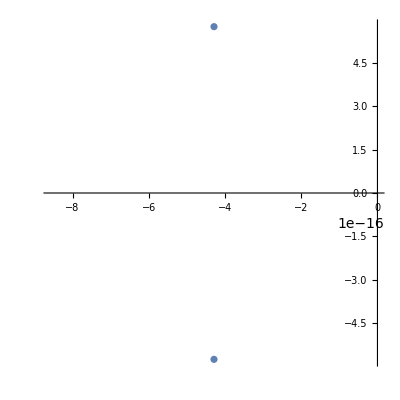

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@EigenvaluesAtFixedPoint,AspectRatio->1]
```

```mathematica
A=ACt^2 (cAMP r1-Dvalue r2)+Km2 (cAMP Km2 r1+Dvalue Km1 r2)
B=4 ACt cAMP Km2 r1 (cAMP r1-Dvalue r2)
C=ACt cAMP r1-cAMP Km2 r1-ACt Dvalue r2-Dvalue Km1 r2
```

```mathematica
JacobianSimplified={{-k3-k2 PDEp-(2 ACt^2 cAMP k1 Km2 r1^2 (-1+Km2/ACt+(2 ACt cAMP Km2 r1-A)/C^2))/(C^2+ACt*Sqrt[B+C^2]),-cAMP k2},{(-PDEp+PDEt) r3/Km3,-((cAMP (Km4+PDEp)^2 r3+Et Km3 Km4 r4)/(Km3 (Km4+PDEp)^2))}}
```